```mathematica
filesAR=FileNames["/home/carla/GDC/CONF/AUS/GDC_Conf_AR_AUS_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/CONF/AUS/GDC_Conf_BR_AUS_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]]
confBR=dataBR[[All,1]]
```

{{{0.0606061,2,33},{0.0588733,0.0606061,0.00184116},{0.944408,0.0606061,4.83069×10^-11,0.00184116}},{{0.2,2,10},{0.198517,0.2,0.00185064},{0.985277,0.2,2.14577×10^-12,0.00185064}},{{1.,1,1},{1.,1.,0.000435964},{1,1.,9.9865×10^-14,0.000435964}}}

{{{0.0162602,2,123},{0.0144362,0.0162602,0.00185064},{0.798284,0.0162602,2.63929×10^-11,0.00185064}},{{0.2,2,10},{0.19851,0.2,0.00185882},{0.985212,0.2,9.9865×10^-13,0.00185882}}}

```mathematica
dojCHEVBKAR=confAR[[All,1]][[All,1]]
dojCHAR=confAR[[All,2]][[All,3]]
dojEVBKAR=confAR[[All,3]][[All,3]]

dojCHEVBKBR=confBR[[All,1]][[All,1]]
dojCHBR=confBR[[All,2]][[All,3]]
dojEVBKBR=confBR[[All,3]][[All,3]]
```

{0.0606061,0.2,1.}

{0.00184116,0.00185064,0.000435964}

{4.83069×10^-11,2.14577×10^-12,9.9865×10^-14}

{0.0162602,0.2}

{0.00185064,0.00185882}

{2.63929×10^-11,9.9865×10^-13}

```mathematica
(*sList={"S0","S1","S2","S3","S4","S5","S6","S7","S8"};
dojP=Labeled[#[[1]],#[[2]]]&/@Map[{doj[[#]],sList[[#]]}&,ran]*)

sList={6,7,8};
sList2={6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];

dojAAR={#[[2]],#[[1]]}&/@Map[{N[dojCHAR[[#]]/dojCHEVBKAR[[#]]],sList[[#]]}&,ran]
dojABR={#[[2]],#[[1]]}&/@Map[{N[dojCHBR[[#]]/dojCHEVBKBR[[#]]],sList2[[#]]}&,ran2]
dojPCHAR={#[[2]],#[[1]]}&/@Map[{dojCHAR[[#]],sList[[#]]}&,ran]
dojPCHBR={#[[2]],#[[1]]}&/@Map[{dojCHBR[[#]],sList2[[#]]}&,ran2]
dojPEVBKAR={#[[2]],#[[1]]}&/@Map[{dojEVBKAR[[#]],sList[[#]]}&,ran]
dojPEVBKBR={#[[2]],#[[1]]}&/@Map[{dojEVBKBR[[#]],sList2[[#]]}&,ran2]
```

{{6,0.0303792},{7,0.00925322},{8,0.000435964}}

{{6.5,0.113815},{7.5,0.00929411}}

{{6,0.00184116},{7,0.00185064},{8,0.000435964}}

{{6.5,0.00185064},{7.5,0.00185882}}

{{6,4.83069×10^-11},{7,2.14577×10^-12},{8,9.9865×10^-14}}

{{6.5,2.63929×10^-11},{7.5,9.9865×10^-13}}

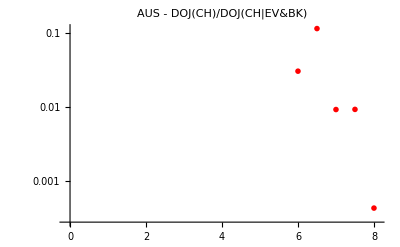

```mathematica
aPlot=ListLogPlot[{Union[dojAAR,dojABR]},  PlotLabel->"AUS - DOJ(CH)/DOJ(CH|EV&BK)", PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red}, PlotRange->All, PlotMarkers->{{"A",12}},ImageSize->400]
chPlot=ListLogPlot[{Union[dojPCHAR,dojPCHBR]}, PlotLegends->{"DOJ(CH)"}, PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red}, PlotRange->All, PlotLabel->"AUS - DOJ(CH)", PlotMarkers->{{"C",12}},ImageSize->400];
evbkPlot=ListLogPlot[{Union[dojPEVBKAR,dojPEVBKBR]}, PlotLegends->{"DOJ(EV&BK)"}, PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Blue}, PlotRange->All, PlotLabel->"AUS - DOJ(EV&BK)", PlotMarkers->{{"E",12}},ImageSize->400];
allPlot=ListLogPlot[{Union[dojPCHAR,dojPCHBR], Union[dojPEVBKAR,dojPEVBKBR]}, PlotLegends->{"DOJ(CH)","DOJ(EV&BK)"}, PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red, Blue}, PlotRange->All, PlotLabel->"AUS - DOJ(CH),DOJ(EV&BK)", PlotMarkers->{{"C",12},{"E",12}},ImageSize->400];
plotsOut=Column[{chPlot,aPlot,evbkPlot} ];
```

```mathematica
SetDirectory["/home/carla/GDC/CONF/AUS/"];
Export["AUS_CH_EVBK.jpeg",plotsOut,ImageResolution->200]
Put[Union[dojPCHAR,dojPCHBR],"AUS_Z_APP.txt"]
Put[Union[dojAAR,dojABR],"AUS_F_APP.txt"]
```

AUS_CH_EVBK.jpeg

```mathematica
(*PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{0, 0.026},  PlotLabel->"AUS - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
Export["AUS_Zoomed_In.jpeg",PlotParts,ImageSize->850]*)
```